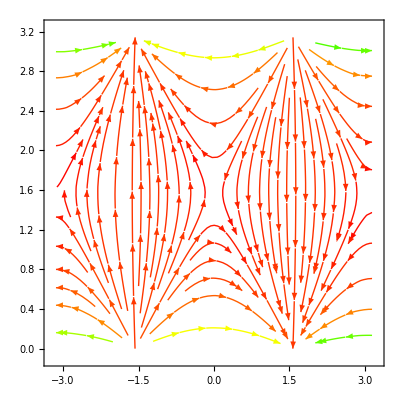
-Graphics--Graphics3D-

```mathematica
sp=StreamPlot[{Cot[θ] Cos[ϕ],-Sin[ϕ]},{ϕ,-π,π},{θ,0,π},StreamColorFunction->Hue,ImageSize->400];

sp3d=Graphics3D[sp[[1]]/.Arrow[z_]:>Arrow[z/.{x_Real,y_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],ImageSize->400];
Row[{sp,sp3d},Spacer[5]]
```

```mathematica
sp=StreamPlot[{Cot[θ] Cos[ϕ],-Sin[ϕ]},{ϕ,-π,π},{θ,0,π},StreamStyle->Arrowheads[{{0.03, Automatic, Graphics[Circle[{0,0},0.01]]}}],StreamColorFunction->Hue,ImageSize->400];

sp3d=Graphics3D[sp[[1]]/.Arrow[z_]:>Arrow[z/.{x_Real,y_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],ImageSize->400];
Row[{sp,sp3d},Spacer[5]]
```

-Graphics--Graphics3D-